1/36 (3-6 y+5 y^2)

1/240 (20-40 y+29 y^2)

1/300 (25-50 y+33 y^2)

1/252 (21-42 y+26 y^2)

1/588 (49-98 y+58 y^2)

(y^2 (40+144 y+203 y^2+144 y^3+40 y^4))/(144 (-1+y)^2 (1+y)^4)

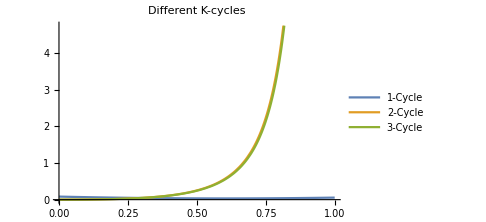

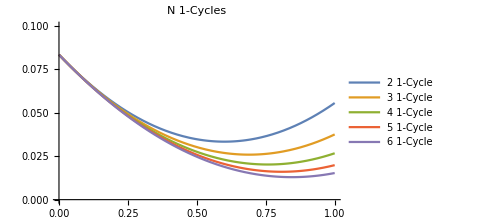

0.277778

0.4125

0.506667

0.575397

0.627551

```mathematica
Clear[y];
twoOneCycle = 1/36 (3-6 y+5 y^2)
threeOneCycle = 1/240 (20-40 y+29 y^2)
fourOneCycle = 1/300 (25-50 y+33 y^2)
fiveOneCycle = 1/252 (21-42 y+26 y^2)
sixOneCycle = 1/588 (49-98 y+58 y^2)
oneOneCycleoneTwoCycle = (y^2 (40+144 y+203 y^2+144 y^3+40 y^4))/(144 (-1+y)^2 (1+y)^4)
oneThreeCycle = (y^2 (40+64 y+99 y^2+64 y^3+40 y^4))/(144 (-1+y^3)^2);
f = (1-y)^2;
 Plot[{twoOneCycle, oneOneCycleoneTwoCycle, oneThreeCycle},{y,0,1}, PlotLabel->"Different K-cycles", ImageSize->Medium, PlotLegends->{"1-Cycle", "2-Cycle", "3-Cycle"}]
Plot[{twoOneCycle, threeOneCycle, fourOneCycle, fiveOneCycle, sixOneCycle},{y,0,1}, PlotRange->{0,.1}, PlotLabel->"N 1-Cycles", ImageSize->Medium, PlotLegends->{"2  1-Cycle", "3 1-Cycle", "4 1-Cycle", "5 1-Cycle", "6 1-Cycle"}, PlotStyle->{Red, Green, Yellow, Blue, Black}]
5/18 //N
33/80 //N
38/75 //N
145/252 //N
123 / 196 //N
```

```mathematica
1/36 (3-6 y+5 y^2)
```

```mathematica
1/240 (20-40 y+29 y^2)
```

```mathematica
1/300 (25-50 y+33 y^2)
```

```mathematica
1/252 (21-42 y+26 y^2)
```

(y^2 (40+144 y+203 y^2+144 y^3+40 y^4))/(144 (-1+y)^2 (1+y)^4)

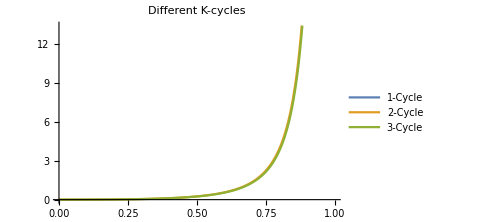

-Graphics-

0.277778

0.4125

0.506667

0.575397

0.627551

0.277778

0.4125

0.506667

0.575397

0.627551

```mathematica
1/588 (49-98 y+58 y^2)
```

```mathematica
(5 y^2)/(18 (-1+y)^2)
```

```mathematica
(33 y^2)/(80 (-1+y)^2)
```

```mathematica
(38 y^2)/(75 (-1+y)^2)
```

```mathematica
(145 y^2)/(252 (-1+y)^2)
```

```mathematica
(123 y^2)/(196 (-1+y)^2)
```